```mathematica
fract0 = Import["fract0.dat"];
```

```mathematica
Min[fract0]
```

0.

```mathematica
boxes[n_,list_] := Table[Floor[2^k list] // DeleteDuplicates // Length ,{k,n}]
```

```mathematica
plotboxes[n_,list_] := ListLogLogPlot[boxes[n,list]]
```

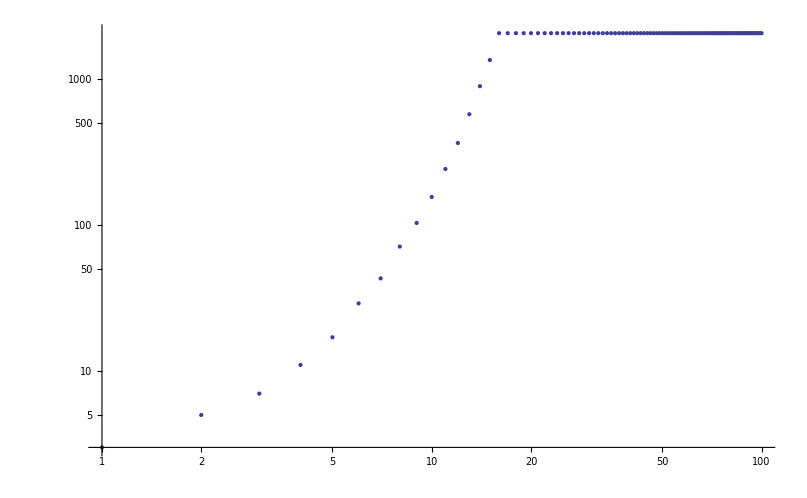

```mathematica
plotboxes[100,fract0]
```

```mathematica
line = Fit[boxes[10000,fract0], {1,x},x]
```

112.559+0.0576596 x

```mathematica
boxes[20,fract0]
```

{2,3,4,5,5,6,7,7,7,9,9,10,11,9,10,11,11,11,13,13}